This notebook has the same formatting as an earlier version of the SCCC Mathematica Tutorial.

sccc package version 2.1

Axes3D, ClearNames, DirectionField, DrawVector, DrawVector3D, EquationPlot, EquationPlot3D, Euler, FunctionTrace, Lim, Line3D, Mag, MakeTable, MakeMultiTable, NumericalIntegration, Point2D, Point3D, RungeKutta, SlopeField, System3D, Taylor, and TF. 
For command description type ?command.

48.75

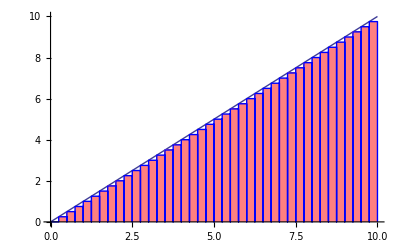

{0,1/4,1/2,3/4,1,5/4,3/2,7/4,2,9/4,5/2,11/4,3,13/4,7/2,15/4,4,17/4,9/2,19/4,5,21/4,11/2,23/4,6,25/4,13/2,27/4,7,29/4,15/2,31/4,8,33/4,17/2,35/4,9,37/4,19/2,39/4}

{0,1/4,1/2,3/4,1,5/4,3/2,7/4,2,9/4,5/2,11/4,3,13/4,7/2,15/4,4,17/4,9/2,19/4,5,21/4,11/2,23/4,6,25/4,13/2,27/4,7,29/4,15/2,31/4,8,33/4,17/2,35/4,9,37/4,19/2,39/4}

1/4

195

{{0,0},{0,0},{1/4,0},{1/4,0},{1/4,0},{1/4,1/4},{1/2,1/4},{1/2,0},{1/2,0},{1/2,1/2},{3/4,1/2},{3/4,0},{3/4,0},{3/4,3/4},{1,3/4},{1,0},{1,0},{1,1},{5/4,1},{5/4,0},{5/4,0},{5/4,5/4},{3/2,5/4},{3/2,0},{3/2,0},{3/2,3/2},{7/4,3/2},{7/4,0},{7/4,0},{7/4,7/4},{2,7/4},{2,0},{2,0},{2,2},{9/4,2},{9/4,0},{9/4,0},{9/4,9/4},{5/2,9/4},{5/2,0},{5/2,0},{5/2,5/2},{11/4,5/2},{11/4,0},{11/4,0},{11/4,11/4},{3,11/4},{3,0},{3,0},{3,3},{13/4,3},{13/4,0},{13/4,0},{13/4,13/4},{7/2,13/4},{7/2,0},{7/2,0},{7/2,7/2},{15/4,7/2},{15/4,0},{15/4,0},{15/4,15/4},{4,15/4},{4,0},{4,0},{4,4},{17/4,4},{17/4,0},{17/4,0},{17/4,17/4},{9/2,17/4},{9/2,0},{9/2,0},{9/2,9/2},{19/4,9/2},{19/4,0},{19/4,0},{19/4,19/4},{5,19/4},{5,0},{5,0},{5,5},{21/4,5},{21/4,0},{21/4,0},{21/4,21/4},{11/2,21/4},{11/2,0},{11/2,0},{11/2,11/2},{23/4,11/2},{23/4,0},{23/4,0},{23/4,23/4},{6,23/4},{6,0},{6,0},{6,6},{25/4,6},{25/4,0},{25/4,0},{25/4,25/4},{13/2,25/4},{13/2,0},{13/2,0},{13/2,13/2},{27/4,13/2},{27/4,0},{27/4,0},{27/4,27/4},{7,27/4},{7,0},{7,0},{7,7},{29/4,7},{29/4,0},{29/4,0},{29/4,29/4},{15/2,29/4},{15/2,0},{15/2,0},{15/2,15/2},{31/4,15/2},{31/4,0},{31/4,0},{31/4,31/4},{8,31/4},{8,0},{8,0},{8,8},{33/4,8},{33/4,0},{33/4,0},{33/4,33/4},{17/2,33/4},{17/2,0},{17/2,0},{17/2,17/2},{35/4,17/2},{35/4,0},{35/4,0},{35/4,35/4},{9,35/4},{9,0},{9,0},{9,9},{37/4,9},{37/4,0},{37/4,0},{37/4,37/4},{19/2,37/4},{19/2,0},{19/2,0},{19/2,19/2},{39/4,19/2},{39/4,0},{39/4,0},{39/4,39/4},{10,39/4},{10,0}}

```mathematica
<<sccc`
(*To do:*)
(*Define a function that takes a function, low/high limits, and number of partitions and calculates the area*)

test[x_]:=(b=x;b=b+1;b=2*b; Return[b] );

f[x_]:=x;

CalculateLeftHand[func_, low_, high_, n_]:= (
dx = (high-low)/n;
xVars = {low};
(*Get each x value*)
Do[xVars = Append[xVars, xVars[[index]]+dx], {index,n-1}];
(*Get the area*)
ret = 0;
Do[ret = ret+(func[xVars[[index]]]), {index, n}];

Return[N[ret*dx]]);
CalculateRightHand[func_, low_, high_, n_]:= func+low+high+n;
CalculateMidPoint[func_, low_, high_, n_]:= func+low+high+n;
CalculateTrapazoid[func_, low_, high_, n_]:= func+low+high+n;
CalculateSimpsonsRule[func_, low_, high_, n_]:= func+low+high+n;

(*Define a function that takes a function, low/high limits, and number of partions and draws the graph with the partitions:*)
DrawLeftHand[func_, low_, high_, n_]:= (
dx = (high-low)/n;
xVars = {low};
(*Get each x value*)
Do[xVars = Append[xVars, xVars[[index]]+dx], {index,n-1}];
yVals = {};
Do[yVals = Append[yVals, func[xVars[[index]]]], {index,n}];

xyList = {};

Do[(
xyList = Append[xyList, {xVars[[index]], 0}];
xyList = Append[xyList, {xVars[[index]], yVals[[index]]}];
xyList = Append[xyList, {xVars[[index]] + dx, yVals[[index]]}];
xyList = Append[xyList, {xVars[[index]] + dx, 0}]), {index, n}];


graph = Plot[func[x], {x, low, high}];

rectanlges = ListPlot[xyList, Joined -> True, Filling->Axis, FillingStyle->Pink, PlotStyle ->{Blue}];

Show[{graph, rectanlges}]
);
DrawRightHand[func_, low_, high_, n_]:= func+low+high+n;
DrawMidPoint[func_, low_, high_, n_]:= func+low+high+n;
DrawTrapazoid[func_, low_, high_, n_]:= func+low+high+n;
DrawSimpsonsRule[func_, low_, high_, n_]:= func+low+high+n;


CalculateLeftHand[f,0,10,40]
DrawLeftHand[f,0,10,40]
xVars
yVals
dx
ret
xyList
```

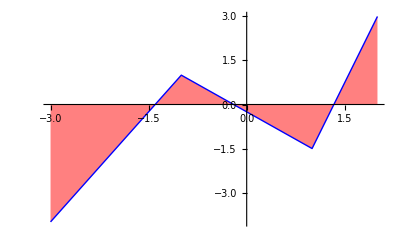

```mathematica
ListPlot[{{-3, -4}, {-1, 1}, {1, -1.5}, {2, 3}}, Joined -> True, Filling->Axis, FillingStyle->Pink, PlotStyle ->{Blue}]
```

```mathematica
Equation1[x_]:= Sqrt[1+x^2]
Equation2[x_]:=ArcTan[x]
Equation3[x_]:=E^(-x^2)
```

```mathematica
Plot[Equation1[x], {x, 0,1}]
```

```mathematica
Plot[Equation2[x], {x, -1,1}]
```

```mathematica
Plot[Equation3[x], {x, 0,1}]
```